{}

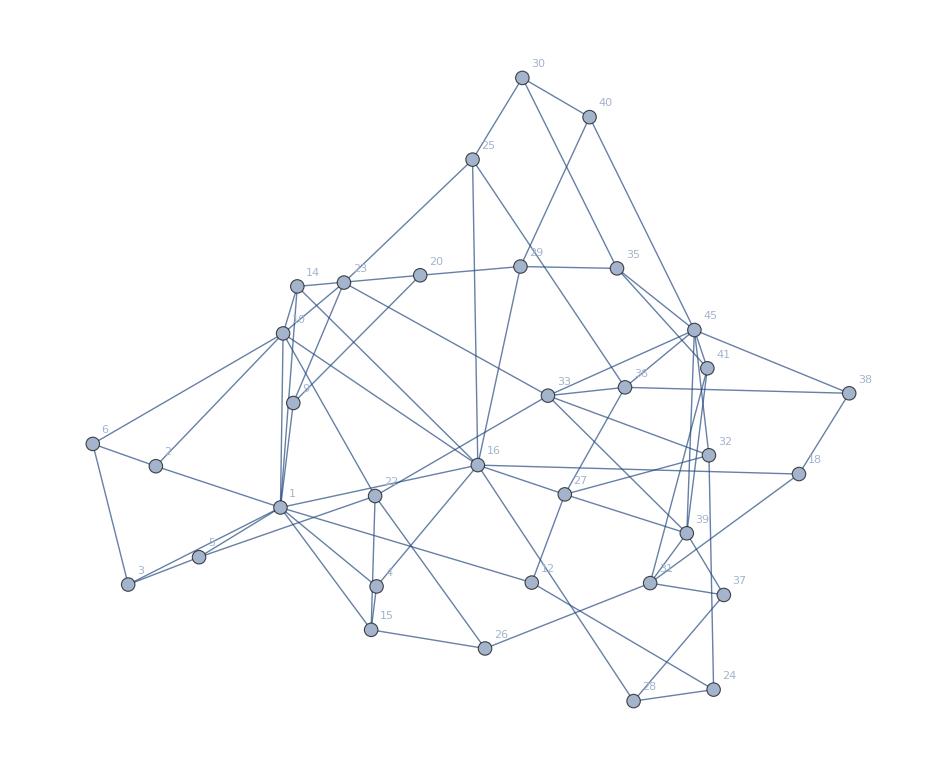

```mathematica
Unprotect[E]
E={{1,2,5},{1,3,11},{1,4,11},{1,5,4},{1,9,5},{1,10,11},{1,12,10},{1,14,12},{1,15,6},{1,16,6},{2,6,4},{2,10,11},{3,5,4},{3,6,11},{4,15,5},{4,16,7},{5,22,10},{6,10,10},{9,20,7},{9,23,10},{10,14,4},{10,16,11},{10,22,9},{10,23,4},{12,24,10},{12,27,5},{14,16,12},{14,20,6},{15,22,9},{15,26,5},{16,18,10},{16,25,11},{16,27,4},{16,28,9},{16,29,7},{18,31,10},{18,38,6},{20,29,4},{22,26,10},{22,33,8},{23,25,8},{23,33,9},{24,28,6},{24,32,9},{25,30,5},{25,36,12},{26,31,6},{27,32,9},{27,36,6},{27,39,6},{28,37,12},{29,35,4},{29,40,7},{30,35,11},{30,40,6},{31,37,5},{31,39,6},{31,41,8},{32,33,9},{32,45,6},{33,36,5},{33,39,10},{33,45,10},{35,41,6},{35,45,5},{36,38,9},{36,45,10},{37,39,4},{38,45,11},{39,41,12},{39,45,10},{40,45,12},{41,45,4}};

(*Edge lists*)
edgeList=Map[Function[x,UndirectedEdge[Part[x,1],Part[x,2]]],E];
(*subGraphs*)

graph=Graph[edgeList];

(*вес*)
For[i=1,i≤Length[E],i++,
graph=SetProperty[{graph,edgeList⟦i⟧},EdgeWeight->E⟦i⟧⟦3⟧];
]

graph=SetProperty[graph,VertexLabels->"Name"];
graph=SetProperty[graph,GraphLayout->{VertexLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}}];
graph
```